# Quantum Random Walk with Two Coins in Entanglement

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx  
Based on work by Salvador Venegas-Andraca

## Introduction

These calculations are reproducing some original calculations by Salvador Venegas-Andraca in his PhD Thesis. You can download those original calculations from this link:

http://homepage.cem.itesm.mx/lgomez/quantum/SalvadorVenegas.pdf

The complete Thesis can be downloaded from Salvador Venegas' web-page:

http://www.mindsofmexico.org/sva/dphil.pdf

http://mindsofmexico.org/sva/vitae.html

## Load the Package

First load the Quantum`Notation` package. Write: 
Needs["Quantum`Notation`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package:

```mathematica
Needs["Quantum`Notation`"]
```

Quantum`Notation` Version 2.2.0. (May 2010) 
A Mathematica package for Quantum calculations in Dirac bra-ket notation
by José Luis Gómez-Muñoz

Execute SetQuantumAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetQuantumAliases[] must be executed again in each new notebook that is created, only one time per notebook.

In order to use the keyboard to enter quantum objects write:
SetQuantumAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQuantumAliases[];
```

## Evolution operator for two coins

Definition of a Hadamard operator

```mathematica
hadamard[j_]:=(|Subscript[0, ĵ]⟩·⟨Subscript[0, ĵ]|+|Subscript[1, ĵ]⟩·⟨Subscript[0, ĵ]|+|Subscript[0, ĵ]⟩·⟨Subscript[1, ĵ]|-|Subscript[1, ĵ]⟩·⟨Subscript[1, ĵ]|)/(√2)
```

This definition is equivalent to equation 6.6 of the PhD thesis of Salvador Venegas-Andraca. The tensor product symbol ⊗ can be entered by pressing the keys [ESC]tp[ESC].

```mathematica
CHEC=Expand[ hadamard[1]⊗hadamard[2] ]
```

1/2 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/2 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/2 |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/2 |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/2 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|-1/2 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+1/2 |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|-1/2 |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+1/2 |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+1/2 |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|-1/2 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|-1/2 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+1/2 |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|-1/2 |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|-1/2 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+1/2 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

## Conditional Shift Operator

This definition is equivalent to equation 6.8 of the PhD thesis of Salvador Venegas-Andraca. The tensor product symbol ⊗ can be entered by pressing the keys [ESC]tp[ESC].

```mathematica
SEC=|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]|⊗∑_(i=-∞)^∞ (|Subscript[(i+1), OverHat[pp]]⟩·⟨Subscript[i, OverHat[pp]]|)+|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|⊗∑_(i=-∞)^∞ (|Subscript[i, OverHat[pp]]⟩·⟨Subscript[i, OverHat[pp]]|)+|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]|⊗∑_(i=-∞)^∞ (|Subscript[i, OverHat[pp]]⟩·⟨Subscript[i, OverHat[pp]]|)+|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|⊗∑_(i=-∞)^∞ (|Subscript[(i-1), OverHat[pp]]⟩·⟨Subscript[i, OverHat[pp]]|)
```

∑_(i=-∞)^∞ |0_OverHat[1],0_OverHat[2],(1+i)_OverHat[pp]⟩·⟨0_OverHat[1],0_OverHat[2],i_OverHat[pp]|+∑_(i=-∞)^∞ |0_OverHat[1],1_OverHat[2],i_OverHat[pp]⟩·⟨0_OverHat[1],1_OverHat[2],i_OverHat[pp]|+∑_(i=-∞)^∞ |1_OverHat[1],0_OverHat[2],i_OverHat[pp]⟩·⟨1_OverHat[1],0_OverHat[2],i_OverHat[pp]|+∑_(i=-∞)^∞ |1_OverHat[1],1_OverHat[2],(-1+i)_OverHat[pp]⟩·⟨1_OverHat[1],1_OverHat[2],i_OverHat[pp]|

## Initial state of the walker

The initial state of the walker is at the origin |0_OverHat[pp]⟩, and the two coins are initially in the maximum-entanglement state (|0_OverHat[1],0_OverHat[2]⟩+|1_OverHat[1],1_OverHat[2]⟩)/(√2). This is the initial stated used for the figure 6.2 of the PhD thesis of Salvador Venegas-Andraca. The tensor product symbol ⊗ can be entered by pressing the keys [ESC]tp[ESC].

```mathematica
|w[0]⟩=|Subscript[0, OverHat[pp]]⟩⊗(|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩)/(√2)
```

(|0_OverHat[1],0_OverHat[2],0_OverHat[pp]⟩+|1_OverHat[1],1_OverHat[2],0_OverHat[pp]⟩)/(√2)

## Calculation of the first three steps of the walker (naive, slow approach)

Here the first three steps of the walker are calculated. Notice the use of the command Expand[]. This evaluation does not produce any output, however the evolution of the system is calculted and stored in |w[1]⟩, |w[2]⟩, and|w[3]⟩

```mathematica
Do[|w[k]⟩=Expand[SEC·(CHEC·|w[k-1]⟩)],
{k,1,3,1}]
```

These are the three steps that were calculated. It is a very good idea to reproduce this first three calculations by hand, without the computer, in order to understand them:

```mathematica
|w[1]⟩
```

(|0_OverHat[1],0_OverHat[2],1_OverHat[pp]⟩)/(√2)+(|1_OverHat[1],1_OverHat[2],(-1)_OverHat[pp]⟩)/(√2)

```mathematica
|w[2]⟩
```

(|0_OverHat[1],0_OverHat[2],0_OverHat[pp]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],2_OverHat[pp]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],(-1)_OverHat[pp]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[pp]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],(-1)_OverHat[pp]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[pp]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],(-2)_OverHat[pp]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[pp]⟩)/(2 √2)

```mathematica
|w[3]⟩
```

(|0_OverHat[1],0_OverHat[2],(-1)_OverHat[pp]⟩)/(4 √2)-(|0_OverHat[1],0_OverHat[2],0_OverHat[pp]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[pp]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],2_OverHat[pp]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],3_OverHat[pp]⟩)/(4 √2)-(|0_OverHat[1],1_OverHat[2],(-2)_OverHat[pp]⟩)/(4 √2)+(|0_OverHat[1],1_OverHat[2],2_OverHat[pp]⟩)/(4 √2)-(|1_OverHat[1],0_OverHat[2],(-2)_OverHat[pp]⟩)/(4 √2)+(|1_OverHat[1],0_OverHat[2],2_OverHat[pp]⟩)/(4 √2)+(|1_OverHat[1],1_OverHat[2],(-3)_OverHat[pp]⟩)/(4 √2)+(|1_OverHat[1],1_OverHat[2],(-2)_OverHat[pp]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],(-1)_OverHat[pp]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[pp]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[pp]⟩)/(4 √2)

## Position Projector

This is the position projector for the j-th position. We will use this operator INSTEAD OF the operators defined in 6.10 and 6.11 of the PhD thesis of Salvador Venegas-Andraca

```mathematica
pospro[j_]:= |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[j, OverHat[pp]]⟩·⟨Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[j, OverHat[pp]]|+|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[j, OverHat[pp]]⟩·⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[j, OverHat[pp]]|+|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[j, OverHat[pp]]⟩·⟨Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[j, OverHat[pp]]|+|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[j, OverHat[pp]]⟩·⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[j, OverHat[pp]]|
```

## Probabilities (naive approach)

Here we calculate the probabilities for the third step.
These are the same numbers as those of the last row of the Table 2, page 114 of the PhD thesis of Salvador Venegas-Andraca

```mathematica
probabilities[3]=
Table[{j,⟨w[3]|·pospro[j]·|w[3]⟩},{j,-3,3}]
```

{{-3,1/32},{-2,3/16},{-1,5/32},{0,1/4},{1,5/32},{2,3/16},{3,1/32}}

This is a plot of the probabilities

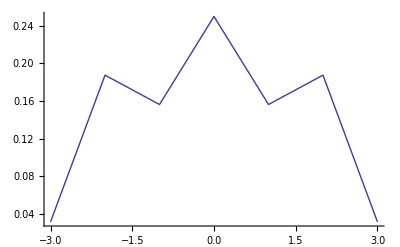

```mathematica
ListPlot[probabilities[3],Joined->True]
```

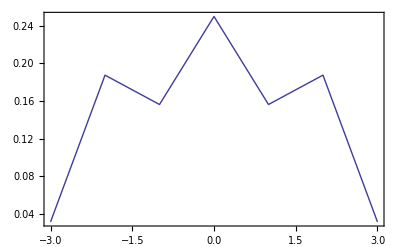

```mathematica
ListPlot[probabilities[3],Joined->True,PlotRange->All,Frame->True,Axes->False]
```

## Calculation of 5 steps of the walker (naive, slow approach)

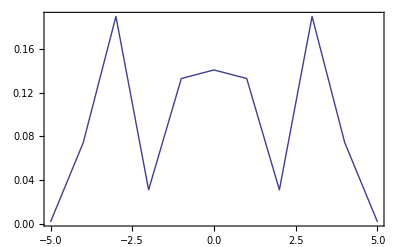
{30.578,-Graphics-}

```mathematica
(* The operators SEC, CHEC and pospro were defined above *)
steps=5;
Timing[
Do[|w[k]⟩=Expand[SEC·(CHEC·|w[k-1]⟩)],
{k,1,steps,1}];
probabilities[steps]=
Table[{j,⟨w[steps]|·pospro[j]·|w[steps]⟩},{j,-steps,steps}];
ListPlot[probabilities[steps],Joined->True,PlotRange->All,Frame->True,Axes->False]
]
```

## Calculation of 5 steps of the walker (efficient, fast approach, more than 20 times faster)

For 5 steps, next approach is more than 20 times faster than the previous one. For larger amount of steps, the difference can be even larger. However, the fast approach uses advanced Mathematica programming:

```mathematica
steps=5;
Timing[
|weff[0]⟩=|Subscript[0, OverHat[pp]]⟩⊗(|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩)/(√2);
Do[
|weff[k]⟩=
Expand[
ReplaceAll[CHEC·|weff[k-1]⟩,
{|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[(j+1), OverHat[pp]]⟩,
|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[(j-1), OverHat[pp]]⟩}]],
{k,1,steps,1}
];
probeff[steps]=Table[
{j,
ketList=
Cases[|weff[steps]⟩,x_.*|Subscript[y_, OverHat[1]],Subscript[z_, OverHat[2]],Subscript[j, OverHat[pp]]⟩];
braList=Map[Function[{w},SuperDagger[(w)]],ketList];
productList=
MapThread[Function[{b,k},b·k],{braList,ketList}];
Apply[Plus,productList]
},
{j,-steps,steps}
];
ListPlot[probeff[steps],Joined->True,PlotRange->All,Frame->True,Axes->False]
]
```

{0.921,-Graphics-}

## Calculation of 200 steps of the walker (efficient approach)

This can take more than one hour in your computer. It reproduces figure 6.3 on page 115 of the PhD thesis of Salvador Venegas-Andraca

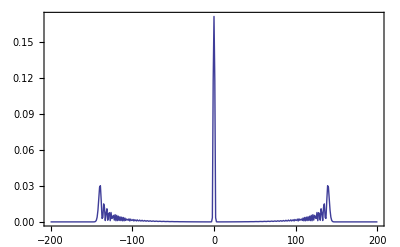

```mathematica
steps=200;
|weff[0]⟩=|Subscript[0, OverHat[pp]]⟩⊗(|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩)/(√2);
Do[
|weff[k]⟩=
Expand[
ReplaceAll[CHEC·|weff[k-1]⟩,
{|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[(j+1), OverHat[pp]]⟩,
|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[j_, OverHat[pp]]⟩:>|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[(j-1), OverHat[pp]]⟩}]],
{k,1,steps,1}
];
probeff[steps]=Table[
{j,
ketList=
Cases[|weff[steps]⟩,x_.*|Subscript[y_, OverHat[1]],Subscript[z_, OverHat[2]],Subscript[j, OverHat[pp]]⟩];
braList=Map[Function[{w},SuperDagger[(w)]],ketList];
productList=
MapThread[Function[{b,k},b·k],{braList,ketList}];
Apply[Plus,productList]
},
{j,-steps,steps}
];
ListPlot[probeff[steps],Joined->True,PlotRange->All,Frame->True,Axes->False]
```

-Graphics-

## References

These calculations are reproducing some original calculations by Salvador Venegas-Andraca in his PhD Thesis. You can download those original calculations from these links:

http://homepage.cem.itesm.mx/lgomez/quantum/SalvadorVenegas.pdf

http://www.mindsofmexico.org/sva/dphil.pdf

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx